## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="PGK";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_PGK";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3pg,Null,Keq substrate}

{1900,Keq value}

{adp,Km or S05 substrate}

{0.000085,Km or S05 value}

{13dpg,Km or S05 substrate}

{0.000011,Km or S05 value}

{atp,Km or S05 substrate}

{0.0035,Km or S05 value}

{3pg,Km or S05 substrate}

{0.0025,Km or S05 value}

{{{adp,Null},{13dpg,Null}},kcat substrates}

{329,kcat value}

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 1900 | 1805.
1995. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 329 | 312.55
345.45 | 1/s | 7 | 25 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,0,0};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;


{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 1900 | 1805.
1995. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 329 | 312.55
345.45 | 1/s | 7 | 25 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
rxn
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

```mathematica
catalyticBranch={"E_PGK[c] + 13dpg[c] <=> E_PGK[c]&13dpg",
				"E_PGK[c]&13dpg + adp[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c] + adp[c] <=> E_PGK[c]&adp",
				"E_PGK[c]&adp + 13dpg[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp",

				"E_PGK[c]&3pg&atp <=> E_PGK[c]&3pg + atp[c]",
				"E_PGK[c]&3pg <=> E_PGK[c] + 3pg[c]",
				
				"E_PGK[c]&3pg&atp <=> E_PGK[c]&atp + 3pg[c]",
				"E_PGK[c]&atp <=> E_PGK[c] + atp[c]"};


enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1,((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2,((PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c)^PGK3,((PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c)^PGK4,((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5,((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c)^PGK7,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c)^PGK8,((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet2={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSet3={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9,  Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet4={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2, catalyticReactionsSet3, catalyticReactionsSet4};
```

## Set up rate equations

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub, otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(13dpg)^c→0,adp^c→0}

{(3pg)^c→0,atp^c→0}

{(13dpg)^c→∞,adp^c→∞}

{(3pg)^c→∞,atp^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
PGKRateConsts=finalRateConsts
Export[inputPath<>"/"<>rxnName<>"_rateConsts.m",PGKRateConsts, "MX"]
```

{k_PGK1^⟵,k_PGK1^⟶,k_PGK2^⟵,k_PGK2^⟶,k_PGK3^⟵,k_PGK3^⟶,k_PGK4^⟵,k_PGK4^⟶,k_PGK5^⟵,k_PGK5^⟶,k_PGK6^⟵,k_PGK6^⟶,k_PGK7^⟵,k_PGK7^⟶,k_PGK8^⟵,k_PGK8^⟶,k_PGK9^⟵,k_PGK9^⟶}

/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/PGK_rateConsts.m

### Setup King-Altman Equations (old)

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
simplifyMaxTime = 100; (*in seconds*)
nActiveSites=1;
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, simplifyMaxTime, nActiveSites];
```

```mathematica
(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getEquivRateConsts[enzymeModel, eqRateConstSub, nonCatalyticReactions];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];


(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

```mathematica
fluxEq = (*unifyRateConstants[*)Total[transitionRateEqs]/.unifiedRateConstList(*]*);(*Flux Will Always Go through the Transition Step*)
		enzForms = Cases[enzymeModel["Species"],_enzyme]//Union;
		enzConservationEq = parameter[rxnName <> "_total"]==Total[enzForms];(*Enzyme Conservation Equation*)

		enzPos = Flatten[Position[enzymeModel["Species"],_enzyme]];
		ssEq = stripTime[enzymeModel["ODE"][[enzPos]]/._'[t]->0];(*Steady State Equations*)
		ssEq = (*unifyRateConstants*)keq2kHT[ssEq]/.unifiedRateConstList;
		
		(*Solve the System for Each Enzyme Form (This May Take Some Time)*)
		enzSol = anonymize[Solve[Join[ssEq,{enzConservationEq}],enzForms]];
		enzSol = keq2kHT[enzSol[[1]]];
		
		(*Apply the Solution to the Flux Equation*)
		absoluteFlux=fluxEq/.enzSol;(*In terms of E_total*)
		absoluteFlux =  parameter["v", rxnName] -> nActiveSites * keq2kHT[anonymize[Simplify[absoluteFlux, TimeConstraint -> simplifyMaxTime]]];
```

Total::normal: Nonatomic expression expected at position 1 in Total[transitionRateEqs].

ReplaceAll::reps: {unifiedRateConstList} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringJoin::string: String expected at position 1 in rxnName<>_total.

ReplaceAll::reps: {unifiedRateConstList} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and List at positions 1 and 2 are expected to be the same.

Solve::naqs: Join[keq2kHT[stripTime[enzymeModel[]]]/.unifiedRateConstList,{parameter[rxnName<>_total]==0}] is not a quantified system of equations and inequalities.

ReplaceAll::reps: {keq2kHT[Solve[Join[keq2kHT[stripTime[enzymeModel[]]]/.unifiedRateConstList,{parameter[StringJoin[«2»]]==0}],{}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Simplify::timc: Number of seconds simplifyMaxTime is not a positive machine-sized number or Infinity.

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	adp[c]	atp[c]	3pg[c]	param_PGK_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/haldaneRatio_4.txt"	1900
1	0.01	8.500000000000002e-6	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.09090909090909091
1	0.01	0.000013471592135919474	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.13680688860321008
1	0.01	0.000021351034667831454	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.20076000891310192
1	0.01	0.000033839109497047245	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.2847472489508013
1	0.01	0.00005363137428081642	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.3868631798468569
1	0.01	0.00008500000000000002	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.5000000000000001
1	0.01	0.00013471592135919474	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.6131368201531432
1	0.01	0.00021351034667831454	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.7152527510491988
1	0.01	0.00033839109497047284	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.7992399910868982
1	0.01	0.0005363137428081642	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.86319311139679
1	0.01	0.0008500000000000003	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_adp.txt"	0.9090909090909092
1	1.100000000000001e-6	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.09090909090909097
1	1.7433825117072269e-6	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.13680688860321014
1	2.7630750746605424e-6	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.200760008913102
1	4.37917887608847e-6	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.2847472489508014
1	6.940530789282128e-6	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.38686317984685703
1	0.000011000000000000008	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.5000000000000002
1	0.00001743382511707227	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.6131368201531434
1	0.000027630750746605424	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.7152527510491988
1	0.00004379178876088469	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.7992399910868982
1	0.00006940530789282128	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.8631931113967901
1	0.00011000000000000009	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/relRateFor_13dpg.txt"	0.9090909090909092
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329
1	0.01	0.01	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/input/absRateFor.txt"	329

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=50;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 1.72217050649
best_fit: 1.09905937713
best_fit: 0.924550537918
best_fit: 0.965393752903
best_fit: 1.09505668621
best_fit: 1.11864605977
best_fit: 1.21469829826
best_fit: 1.0941373178
best_fit: 1.27537603927
best_fit: 1.09056306996
best_fit: 1.36379089761
best_fit: 1.28452203997
best_fit: 1.04513312853
best_fit: 2.20030572413
best_fit: 1.09583152955
best_fit: 1.21332267007
best_fit: 1.07748693632
best_fit: 1.09382787937
best_fit: 1.08636416552
best_fit: 1.07920722715
best_fit: 1.08884094364
best_fit: 1.06282957389
best_fit: 1.09368447599
best_fit: 1.09121464402
best_fit: 1.1866584628
best_fit: 1.09062704433
best_fit: 1.09803938858
best_fit: 1.18543483087
best_fit: 4.02314879124
best_fit: 1.06841354751
best_fit: 1.09126895388
best_fit: 1.16592550784
best_fit: 1.05026580491
best_fit: 1.28328412878
best_fit: 0.923848303338
best_fit: 0.448762462027
best_fit: 0.988896539696
best_fit: 3.00303446255
best_fit: 1.09860990956
best_fit: 1.09649370777
best_fit: 1.09839908981
best_fit: 1.01376367574
best_fit: 1.09522781174
best_fit: 1.09317116785
best_fit: 0.80540012364
best_fit: 1.22644012919
best_fit: 1.05978712599
best_fit: 0.952895491513
best_fit: 1.09992310706
best_fit: 1.20396721336

## Evaluate fit results

```mathematica
lmaResultsFileNew="/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGK/fit_PGK/output/raw/lmaResults_PGK_2017823941.txt";
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_1 | 1.28284×10^-11 | 1.64568×10^-22 | 5.61254×10^-8 | 2.95397×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_2 | 2.28288×10^-11 | 5.21156×10^-22 | 9.98762×10^-8 | 5.25664×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_3 | 1.71716×10^-11 | 2.94864×10^-22 | 7.5122×10^-8 | 3.95379×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | haldaneRatio_4 | 7.17115×10^-12 | 5.14254×10^-23 | 3.13714×10^-8 | 1.65113×10^-9 | 1900 | 1900.
1 | relRateFor_adp | 0.0000889049 | 7.90409×10^-9 | 0.000018612 | 0.0204732 | 0.0909091 | 0.0909277
1 | relRateFor_adp | 0.0000472545 | 2.23299×10^-9 | 0.0000148864 | 0.0108813 | 0.136807 | 0.136822
1 | relRateFor_adp | 0.0000219979 | 4.83907×10^-10 | 0.0000101692 | 0.00506533 | 0.20076 | 0.20077
1 | relRateFor_adp | 7.38572×10^-6 | 5.45489×10^-11 | 4.84253×10^-6 | 0.00170064 | 0.284747 | 0.284752
1 | relRateFor_adp | 3.27343×10^-7 | 1.07154×10^-13 | 2.91592×10^-7 | 0.0000753735 | 0.386863 | 0.386863
1 | relRateFor_adp | 3.69483×10^-6 | 1.36518×10^-11 | 4.25382×10^-6 | 0.000850763 | 0.5 | 0.499996
1 | relRateFor_adp | 4.53282×10^-6 | 2.05464×10^-11 | 6.3994×10^-6 | 0.00104371 | 0.613137 | 0.61313
1 | relRateFor_adp | 4.11395×10^-6 | 1.69246×10^-11 | 6.77535×10^-6 | 0.000947267 | 0.715253 | 0.715246
1 | relRateFor_adp | 3.2465×10^-6 | 1.05397×10^-11 | 5.97456×10^-6 | 0.00074753 | 0.79924 | 0.799234
1 | relRateFor_adp | 2.36108×10^-6 | 5.57468×10^-12 | 4.69281×10^-6 | 0.000543657 | 0.863193 | 0.863188
1 | relRateFor_adp | 1.63133×10^-6 | 2.66124×10^-12 | 3.41479×10^-6 | 0.000375627 | 0.909091 | 0.909087
1 | relRateFor_13dpg | 0.000381932 | 1.45872×10^-7 | 0.0000799834 | 0.0879818 | 0.0909091 | 0.0909891
1 | relRateFor_13dpg | 0.000348825 | 1.21679×10^-7 | 0.000109927 | 0.0803522 | 0.136807 | 0.136917
1 | relRateFor_13dpg | 0.000302698 | 9.16262×10^-8 | 0.000139976 | 0.0697231 | 0.20076 | 0.2009
1 | relRateFor_13dpg | 0.000242129 | 5.86266×10^-8 | 0.000158798 | 0.0557679 | 0.284747 | 0.284906
1 | relRateFor_13dpg | 0.000168498 | 2.83916×10^-8 | 0.000150125 | 0.0388056 | 0.386863 | 0.387013
1 | relRateFor_13dpg | 0.0000869345 | 7.55762×10^-9 | 0.000100097 | 0.0200194 | 0.5 | 0.5001
1 | relRateFor_13dpg | 5.3864×10^-6 | 2.90133×10^-11 | 7.60456×10^-6 | 0.00124027 | 0.613137 | 0.613144
1 | relRateFor_13dpg | 0.0000682048 | 4.6519×10^-9 | 0.00011232 | 0.0157035 | 0.715253 | 0.71514
1 | relRateFor_13dpg | 0.000128722 | 1.65694×10^-8 | 0.000236854 | 0.029635 | 0.79924 | 0.799003
1 | relRateFor_13dpg | 0.000174798 | 3.05543×10^-8 | 0.000347354 | 0.0402406 | 0.863193 | 0.862846
1 | relRateFor_13dpg | 0.000207863 | 4.32069×10^-8 | 0.000435006 | 0.0478507 | 0.909091 | 0.908656
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.
1 | absRateFor | 6.83009×10^-13 | 4.66502×10^-25 | 5.17673×10^-10 | 1.57347×10^-10 | 329 | 329.

### Simulated Data and Best Fit Data Plot

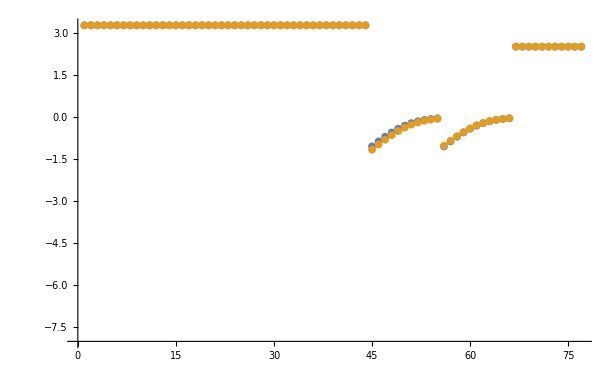

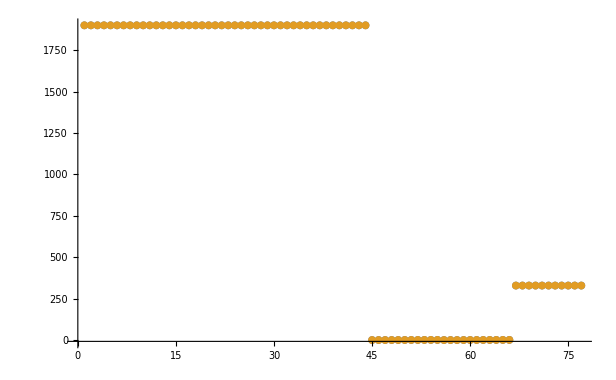

```mathematica
datasetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

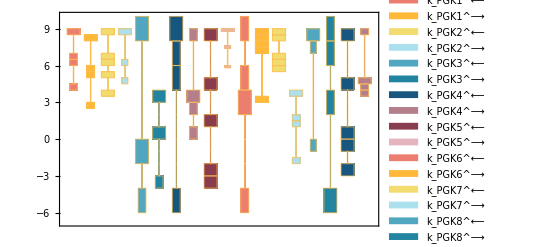

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

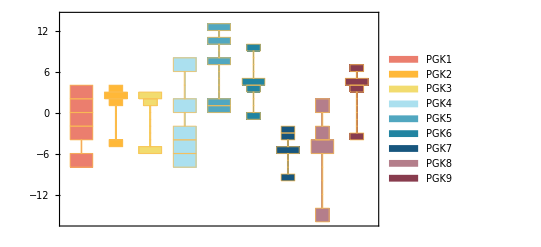

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

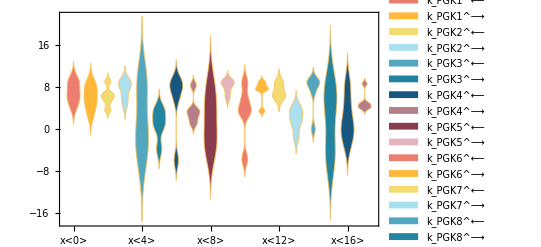

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000085 | -0.0357233
0.0000834187 | 42127.4
1.86035
0.000011 | -3039.75
0.0000123938 | 2.76341×10^10
12.6711

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
329 | 329. | 1.51879×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1700 | 1700. | 0.0000148583